# A Quantum-Like for the International Interaction Game

## The International Interaction Backward Induction Model

Explain here the Signorino  tree based model
-Graphics-

## A Quantum-Like Approach

### Backward Induction Functions - Classical Setting

```mathematica
$RecursionLimit=10000;
```

```mathematica
q10cl[U2War1_,U2Cap2_]:=ⅇ^U2War1/(ⅇ^U2War1+ⅇ^U2Cap2) ;
```

```mathematica
notq10cl[U2War1_,U2Cap2_]:=1-q10cl[U2War1,U2Cap2];
```

```mathematica
q11cl[U2War1_,U2Cap2_]:=  q10cl[U2War1,U2Cap2];
```

```mathematica
notq11cl[U2War1_,U2Cap2_]:=  notq10cl[U2War1,U2Cap2];
```

```mathematica
p8cl[U1War2_,U1Cap1_] :=ⅇ^U1War2/(ⅇ^U1War2+ⅇ^U1Cap1);
```

```mathematica
notp8cl[U1War2_,U1Cap1_]:=1 - p8cl[U1War2,U1Cap1];
```

```mathematica
p12cl[U1War2_,U1Cap1_]:= p8cl[U1War2,U1Cap1];
```

```mathematica
notp12cl[U1War2_,U1Cap1_]:= notp8cl[U1War2,U1Cap1];
```

```mathematica
q9cl[U1War2_,U1Cap1_,U2War2_,U2Cap1_, U2Nego_]:= Module[{UP2N12,p12, notp12},
p12=p12cl[U1War2,U1Cap1];
notp12=notp12cl[U1War2,U1Cap1];
UP2N12= p12 U2War2 + notp12 U2Cap1;
ⅇ^UP2N12/(ⅇ^UP2N12+ⅇ^U2Nego)
];
```

```mathematica
notq9cl[U1War2_,U1Cap1_,U2War2_,U2Cap1_, U2Nego_]:= 1-q9cl[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
```

```mathematica
notq9cl[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
```

```mathematica
p7cl[U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_]:= Module[{UP1N11, q11, notq11},
q11 = q11cl[U2War1,U2Cap2];
notq11=notq11cl[U2War1,U2Cap2];
UP1N11=q11 U1War1+notq11 U1Cap2;
ⅇ^UP1N11/(ⅇ^UP1N11+ⅇ^U1Nego)
];
```

```mathematica
notp7cl[U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_]:= 1-p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
```

```mathematica
q6cl[U1War1_, U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_]:= Module[{UP2N8,U2N11, UP2N7, p8,notp8,p7,notp7,q11,notq11},
p8=p8cl[U1War2,U1Cap1];
notp8=notp8cl[U1War2,U1Cap1];
notp7=notp7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
p7=p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
UP2N8=p8 U2War2+notp8 U2Cap1;
q11=q11cl[U2War1,U2Cap2];
notq11=notq11cl[U2War1,U2Cap2];
U2N11=q11 U2War1+notq11 U2Cap2;
UP2N7=p7 U2N11+notp7 U2Nego;
ⅇ^UP2N8/(ⅇ^UP2N8+ⅇ^UP2N7)
];
```

```mathematica
notq6cl[U1War1_, U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_]:= 1-q6cl[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
```

```mathematica
p5cl[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_]:=Module[{UP1N10,UP2N10,UP2N9,UP1N9,q10,notq10,q9,notq9,p12,notp12,UP1N12},
p12=p12cl[U1War2,U1Cap1];
notp12=notp12cl[U1War2,U1Cap1];
UP1N12=p12 U1War2 + notp12 U1Cap1;
q10=q10cl[U2War1,U2Cap2];
notq10=notq10cl[U2War1,U2Cap2];
q9=q9cl[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
notq9=notq9cl[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
UP1N10=q10 U1War1+notq10 U1Cap2;
UP1N9=q9 UP1N12+notq9 U1Nego;
ⅇ^UP1N10/(ⅇ^UP1N10+ⅇ^UP1N9)
];
```

```mathematica
notp5cl[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_]:=1-p5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
```

```mathematica
p4cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_]:=Module[{UP1N6,q11,notq11,p8,notp8,p7,notp7,q6,notq6,UP1N11,UP1N8,UP1N7},
q11=q11cl[U2War1,U2Cap2];
notq11=notp12cl[U2War1,U2Cap2];

p8=p8cl[U1War2,U1Cap1];
notp8 = notp8cl[U1War2,U1Cap1];

p7=p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

q6=q6cl[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6cl[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

UP1N11=q11 U1War1+notq11 U1Cap2;
UP1N8=p8 U1War2+notp8 U1Cap1;
UP1N7=p7 UP1N11+notp7 U1Nego;
UP1N6=q6 UP1N8+notq6 UP1N7;
ⅇ^UP1N6/(ⅇ^UP1N6+ⅇ^U1Acq1)
];
```

```mathematica
notp4cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_]:=1-p4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];
```

```mathematica
q3cl[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_,U2Acq2_]:=Module[{UP2N12,UP2N10,UP2N9,UP2N5,p12,notp12,q10,notq10,q9,notq9,p5,notp5},
p12=p12cl[U1War2,U1Cap1];
notp12=notp12cl[U1War2,U1Cap1];
UP2N12=p12 U2War2 + notp12 U2Cap1;

q10=q10cl[U2War1,U2Cap2];
notq10=notq10cl[U2War1,U2Cap2];
UP2N10=q10 U2War1+notq10 U2Cap2;

q9=q9cl[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
notq9=notq9cl[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
UP2N9=q9 UP2N12+notq9 U2Nego;

p5=p5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
notp5=notp5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
UP2N5=p5 UP2N10+notp5 UP2N9;
ⅇ^UP2N5/(ⅇ^UP2N5+ⅇ^U2Acq2)
];
```

```mathematica
notq3cl[U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_,U2Acq2_]:=1-q3cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];
```

```mathematica
q2cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_]:=Module[{UP2N4,q11,notq11,p7,notp7,p8,notp8,q6,notq6,p4,notp4,UP2N11,UP2N7,UP2N8,UP2N6},
q11=q11cl[U2War1,U2Cap2];
notq11=notq11cl[U2War1,U2Cap2];

p7=p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

p8=p8cl[U1War2,U1Cap1];
notp8=notp8cl[U1War2,U1Cap1];

q6=q6cl[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6cl[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p4=p4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];
notp4=notp4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

UP2N11=q11 U2War1+notq11 U2Cap2;
UP2N7=p7 UP2N11+notp7 U2Nego;
UP2N8=p8 U2War2+notp8 U2Cap1;
UP2N6= q6 UP2N8+notq6 UP2N7;
UP2N4=p4 UP2N6+notp4 U2Acq1;
ⅇ^UP2N4/(ⅇ^UP2N4+ⅇ^U2SQ)
];
```

```mathematica
notq2cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_]:=1-q2cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];
```

```mathematica
p1cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{UP1N2,UP1N3,UP1N4,UP1N5,UP1N6,UP1N9,UP1N10,UP1N12,q2,notq2,q3,notq3,p4,notp4,p5,notp5,q6,notq6,p8,notp8,p7,notp7,q9,notq9,q10,notq10,q11,notq11,p12,notp12, UP1N11,UP1N7,UP1N8},

p12=p12cl[U1War2,U1Cap1];
notp12=notp12cl[U1War2,U1Cap1];
p8=p8cl[U1War2,U1Cap1];
notp8=notp8cl[U1War2,U1Cap1];
q11=q11cl[U2War1,U2Cap2];
notq11=notq11cl[U2War1,U2Cap2];

q10=q10cl[U2War1,U2Cap2];
notq10=notp12cl[U2War1,U2Cap2];

q9=q9cl[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
notq9=notq9cl[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

p7=p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notp7=notp7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

q6=q6cl[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
notq6=notq6cl[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p5 =p5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
notp5=notp5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

p4=p4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];
notp4=notp4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

q3=q3cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];
notq3=notq3cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

q2=q2cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];
notq2=notq2cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

UP1N12=p12 U1War1+notp12 U1Cap1;
UP1N11=q11 U1War1+notq11 U1Cap2;
UP1N9=q9 UP1N12+notq9 U1Nego;

UP1N7=p7 UP1N11+notp7 U1Nego;
UP1N8=p8 U2War2+notp8 U2Cap1;

UP1N10=q10 U1War1+notq10 U1Cap2;
UP1N6= q6 UP1N8+notq6 UP1N7;

UP1N5=p5 UP1N10+notp5 UP1N9;
UP1N4=p4 UP1N6+notp4 U1Acq1;

UP1N3=q3 UP1N5+notq3 U1Acq2;
UP1N2=q2 UP1N4+notq2 U1SQ;
ⅇ^UP1N3/(ⅇ^UP1N3+ⅇ^UP1N2)
];
```

```mathematica
notp1cl[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=1-p1cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
```

now probability amplitudes

```mathematica
p12quantum [U1War2_,U1Cap1_]:= Module [{p12clprob},
p12clprob = p12cl[U1War2,U1Cap1];
Sqrt[p12clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
notp12quantum [U1War2_,U1Cap1_]:= Module [{notp12clprob},
notp12clprob = notp12cl[U1War2,U1Cap1];
Sqrt[notp12clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
q11quantum [U2War1_,U2Cap2_]:= Module [{q11clprob},
q11clprob = q11cl[U2War1,U2Cap2];
Sqrt[q11clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
notq11quantum [U2War1_,U2Cap2_]:= Module [{notq11clprob},
notq11clprob = notq11cl[U2War1,U2Cap2];
Sqrt[notq11clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
q10quantum [U2War1_,U2Cap2_]:= Module [{q10clprob},
q10clprob = q10cl[U2War1,U2Cap2];
Sqrt[q10clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
notq10quantum [U2War1_,U2Cap2_]:= Module [{notq10clprob},
notq10clprob = notq10cl[U2War1,U2Cap2];
Sqrt[notq10clprob] ⅇ^(ⅈ Re[θ2]) (*  ⅇ^(ⅈ Re[θ2+π/2]) *)
];
```

```mathematica
q9quantum [U1War2_,U1Cap1_,U2War2_,U2Cap1_, U2Nego_]:= Module [{q9clprob},
q9clprob = q9cl[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
Sqrt[q9clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
notq9quantum [U1War2_,U1Cap1_,U2War2_,U2Cap1_, U2Nego_]:= Module [{notq9clprob},
notq9clprob = notq9cl[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];
Sqrt[notq9clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
p8quantum [U1War2_,U1Cap1_]:= Module [{p8clprob},
p8clprob = p8cl[U1War2,U1Cap1];
Sqrt[p8clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
notp8quantum [U1War2_,U1Cap1_]:= Module [{notp8clprob},
notp8clprob = notp8cl[U1War2,U1Cap1];
Sqrt[notp8clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
p7quantum [U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_]:= Module [{p7clprob},
p7clprob = p7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
Sqrt[p7clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
notp7quantum [U1War1_,U1Cap2_,U2War1_,U2Cap2_,U1Nego_]:= Module [{notp7clprob},
notp7clprob = notp7cl[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
Sqrt[notp7clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
q6quantum [U1War1_, U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_]:= Module [{q6clprob},
q6clprob = q6cl[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
Sqrt[q6clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
notq6quantum [U1War1_, U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U2War1_,U2Cap2_,U1Nego_,U2Nego_]:= Module [{notq6clprob},
notq6clprob = notq6cl[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];
Sqrt[notq6clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
p5quantum [U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_]:= Module [{p5clprob},
p5clprob = p5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
Sqrt[p5clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
notp5quantum [U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_]:= Module [{notp5clprob},
notp5clprob = notp5cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];
Sqrt[notp5clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
p4quantum [U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_]:= Module [{p4clprob},
p4clprob = p4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];
Sqrt[p4clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
notp4quantum [U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_]:= Module [{notp4clprob},
notp4clprob = notp4cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];
Sqrt[notp4clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
q3quantum [U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_,U2Acq2_]:= Module [{q3clprob},
q3clprob = q3cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];
Sqrt[q3clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
notq3quantum [U1Cap1_,U2Cap1_,U1Cap2_,U2Cap2_,U1War1_,U2War1_,U1War2_,U2War2_, U1Nego_,U2Nego_,U2Acq2_]:= Module [{notq3clprob},
notq3clprob = notq3cl[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];
Sqrt[notq3clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
q2quantum [U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_]:= Module [{q2clprob},
q2clprob = q2cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];
Sqrt[q2clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
notq2quantum [U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U2SQ_]:= Module [{notq2clprob},
notq2clprob = notq2cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];
Sqrt[notq2clprob] ⅇ^(ⅈ Re[θ2])
];
```

```mathematica
p1quantum [U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:= Module [{p1clprob},
p1clprob = p1cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
Sqrt[p1clprob] ⅇ^(ⅈ Re[θ1])
];
```

```mathematica
notp1quantum [U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:= Module [{notp1clprob},
notp1clprob = notp1cl[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
Sqrt[notp1clprob] ⅇ^(ⅈ Re[θ1])
];
```

### Backward Induction Outcome Functions - Quantum-Like Setting

```mathematica
SQquantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:= Module[{term1,conjugate,notp1,notq2},

notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

notq2=notq2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

term1= notp1 notq2;
conjugate=Conjugate[term1];
term1 conjugate
];
```

```mathematica
ACQ1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{notp1,q2,notq2,notp4,term1,conjugate},
notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

notp4=notp4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

term1= notp1 q2 notp4 ;
conjugate=Conjugate[term1];
term1 conjugate
];
```

```mathematica
ACQ2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{p1,notq3,term1,conjugate},
p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

notq3=notq3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

term1= p1 notq3;
conjugate=Conjugate[term1];
term1 conjugate
];
```

```mathematica
(* ------------- Probability for Negotiation --------------------------- *)
```

```mathematica
NEGOquantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{p1,notp1,q2,q3,p4,notp5,notq6,notp7,notq9,term1, conjugate},
p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];
notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

q3 =q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

notp7=notp7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];
notq9=notq9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

(* ((1-p1) q2 p4 (1-q6) (1-p7) + p1 q3 (1-p5) (1-q9)) *)
term1=notp1 q2 p4 notq6 notp7 +p1 q3 notp5 notq9;
conjugate=Conjugate[term1];
term1 conjugate
];
```

```mathematica
(* ------------- Probability for CAP 1 ---------------------------------- *)
```

```mathematica
CAP1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{notp1,p1,q2,p4,q6,notp8,q3,notp5,q9,notp12,term1, conjugate},

notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

q6=q6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

notp8=notp8quantum[U1War2,U1Cap1];

p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q3 =q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

notp12=notp12quantum[U1War2,U1Cap1];

term1= notp1 q2 p4 q6 notp8 + p1 q3 notp5 q9 notp12;
conjugate=Conjugate[term1];
 term1 conjugate
];
```

```mathematica
(* ------------- Probability for CAP 2 ---------------------------------- *)
```

```mathematica
CAP2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_]:=Module[{notp1,q2,p1,p4,notq6,q6,p7,notp8,q3,notp5,q9,notp12,notq11,term1, conjugate, p5, notq10},

notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

notp8=notp8quantum[U1War2,U1Cap1];

p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q3 =q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

p5=p5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

notp12=notp12quantum[U1War2,U1Cap1];

notq11=notq11quantum[U2War1,U2Cap2];

notq10=notq10quantum[U2War1,U2Cap2];

term1= notp1 q2 p4 notq6 p7 notq11 + p1 q3 p5 notq10;
conjugate=Conjugate[term1];
 term1 conjugate
];
```

```mathematica
(* ------------- Probability for WAR 1 ---------------------------------- *)
```

```mathematica
WAR1quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_] := Module[{notp1,p1, q2, p4,notq6, p7,q11,q3,q10, p5, term1, conjugate},

notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

notq6=notq6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

p7=p7quantum[U1War1,U1Cap2,U2War1,U2Cap2,U1Nego];

q11=q11quantum[U2War1,U2Cap2];

q3 =q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

q10=q10quantum[U2War1,U2Cap2];

p5=p5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

(* ((1-p1)q2 p4 (1-q6) p7 q11 + p1 q3 p5 q10  )  *)
term1 = notp1 q2 p4 notq6 p7 q11 + p1 q3 p5 q10;
conjugate = Conjugate[term1];
 term1 conjugate
];
```

```mathematica
(* ------------- Probability for WAR 2 ---------------------------------- *)
```

```mathematica
WAR2quantum[U1War2_,U1Cap1_,U1Cap2_,U2War2_,U2Cap1_,U1War1_,U2War1_,U2Cap2_, U1Nego_,U2Nego_,U1Acq1_,U2Acq1_,U1Acq2_,U2Acq2_,U1SQ_,U2SQ_] := Module[{notp1,p1, q2, p4,q6,q11,p8,q3,q10, notp5, q9,p12,term1, conjugate},

notp1=notp1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

p1=p1quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U1Acq2,U2Acq2,U1SQ,U2SQ];

q2=q2quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1,U2Acq1,U2SQ];

p4=p4quantum[U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U1War1,U2War1,U2Cap2, U1Nego,U2Nego,U1Acq1];

q6=q6quantum[U1War1, U1War2,U1Cap1,U1Cap2,U2War2,U2Cap1,U2War1,U2Cap2,U1Nego,U2Nego];

q11=q11quantum[U2War1,U2Cap2];

p8=p8quantum[U1War2,U1Cap1];

q3 =q3quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego,U2Acq2];

q10=q10quantum[U2War1,U2Cap2];

notp5=notp5quantum[U1Cap1,U2Cap1,U1Cap2,U2Cap2,U1War1,U2War1,U1War2,U2War2, U1Nego,U2Nego];

q9=q9quantum[U1War2,U1Cap1,U2War2,U2Cap1, U2Nego];

p12=p12quantum[U1War2,U1Cap1];

(* (((1-p1) q2 p4 q6 p8 + p1 q3 (1-p5) q9 p12)  *)
term1 = notp1 q2 p4 q6 p8  + p1 q3 notp5 q9 p12;
conjugate = Conjugate[term1];
 term1 conjugate
];
```

### Visualisation

```mathematica
makeplot[Outcome_, x_,y_,title_]:= Plot3D[Re[Outcome],{θ1,0, 2 π},{θ2,0, 2 π},PlotRange->All,ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style["θ_Player1",16],Style["θ_Player2",16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12],PlotLabel->title]
```

### The Dataset

```mathematica
data = Import["/Users/162191/Documents/GitHub/quantum_international_interaction_game/Norm_Form/first_dataset_with_SQ.csv"];
```

```mathematica
numCols = Length[data[[1]]]
```

19

```mathematica
numRows=Length[data]
```

752

```mathematica
θ1=0;
θ1 = 2 π;
```

```mathematica
(* Dataset row *)
```

```mathematica
i=3;
```

```mathematica
Clear[θ1,θ1, INTEVX, INTEVY];
(* Player ID *)
Player1=data[[i,1]];
Player2=data[[i,2]];

Print["Loading Player ", Player1," and ", Player2];

(* Utilities for Player 1 *)
U1SQ = data[[i,3]];
U1Acq1 = data[[i,4]];
U1Acq2=data[[i,5]];
U1Nego=data[[i,6]];
U1Cap1=data[[i,7]];
U1Cap2=data[[i,8]];
U1War1=data[[i,9]];
U1War2=data[[i,10]];

Print["P1 U1SQ ", U1SQ]
Print["P1 U1Acq1 ", U1Acq1]
Print["P1 U1Acq2 ", U1Acq2]
Print["P1 U1Nego ", U1Nego]
Print["P1 U1Cap1 ", U1Cap1]
Print["P1 U1Cap2 ", U1Cap2]
Print["P1 U1War1 ", U1War1]
Print["P1 U1War2 ", U1War2]


(* Player 2 utilities *)
U2SQ = data[[i,11]];
U2Acq2 = data[[i,12]];
U2Acq1=data[[i,13]];
U2Nego=data[[i,14]];
U2Cap2=data[[i,15]];
U2Cap1=data[[i,16]];
U2War2=data[[i,17]];
U2War1=data[[i,18]];

(* Groundtruth *)
Grountruth=data[[i,19]];
Print["Groundtruth: ", Grountruth];

(* Compute Quantum Probabilities for Different Outcomes *)
```

Loading Player RUS and TUR

P1 U1SQ 0.988028

P1 U1Acq1 -1.02

P1 U1Acq2 1.92768

P1 U1Nego -0.096173

P1 U1Cap1 -1.70659

P1 U1Cap2 1.61802

P1 U1War1 -0.749125

P1 U1War2 -1.09242

Groundtruth: Nego

```mathematica
SQ = SQquantum[U1War2, U1Cap1, U1Cap2, U2War2, U2Cap1, U1War1, U2War1, U2Cap2, U1Nego, U2Nego, U1Acq1, U2Acq1, U1Acq2, U2Acq2, U1SQ, U2SQ];
```

```mathematica
Print["Computing*probabilities"]
SQ = SQquantum[U1War2, U1Cap1, U1Cap2, U2War2, U2Cap1, U1War1, U2War1, U2Cap2, U1Nego, U2Nego, U1Acq1, U2Acq1, U1Acq2, U2Acq2, U1SQ, U2SQ]; 
ACQ1 = ACQ1quantum[U1War2, U1Cap1, U1Cap2, U2War2, U2Cap1, U1War1, U2War1, U2Cap2, U1Nego, U2Nego, U1Acq1, U2Acq1, U1Acq2, U2Acq2, U1SQ, U2SQ]; 
ACQ2 = ACQ2quantum[U1War2, U1Cap1, U1Cap2, U2War2, U2Cap1, U1War1, U2War1, U2Cap2, U1Nego, U2Nego, U1Acq1, U2Acq1, U1Acq2, U2Acq2, U1SQ, U2SQ]; 
NEGO = NEGOquantum[U1War2, U1Cap1, U1Cap2, U2War2, U2Cap1, U1War1, U2War1, U2Cap2, U1Nego, U2Nego, U1Acq1, U2Acq1, U1Acq2, U2Acq2, U1SQ, U2SQ]; 
CAP1 = CAP1quantum[U1War2, U1Cap1, U1Cap2, U2War2, U2Cap1, U1War1, U2War1, U2Cap2, U1Nego, U2Nego, U1Acq1, U2Acq1, U1Acq2, U2Acq2, U1SQ, U2SQ]; 
CAP2 = CAP2quantum[U1War2, U1Cap1, U1Cap2, U2War2, U2Cap1, U1War1, U2War1, U2Cap2, U1Nego, U2Nego, U1Acq1, U2Acq1, U1Acq2, U2Acq2, U1SQ, U2SQ]; 
WAR1 = WAR1quantum[U1War2, U1Cap1, U1Cap2, U2War2, U2Cap1, U1War1, U2War1, U2Cap2, U1Nego, U2Nego, U1Acq1, U2Acq1, U1Acq2, U2Acq2, U1SQ, U2SQ]; 
WAR2 = WAR2quantum[U1War2, U1Cap1, U1Cap2, U2War2, U2Cap1, U1War1, U2War1, U2Cap2, U1Nego, U2Nego, U1Acq1, U2Acq1, U1Acq2, U2Acq2, U1SQ, U2SQ];
```

Computing*probabilities

```mathematica
Print["Normalizing probabilities"]
SQnorm = Re[SQ / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2)];
ACQ1norm = Re[ACQ1 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2)];
ACQ2norm = Re[ACQ2 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2)];
NEGOnorm = Re[NEGO / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2)];
CAP1norm = Re[CAP1 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2)];
CAP2norm = Re[CAP2 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2)];
WAR1norm = Re[WAR1 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2)];
WAR2norm = Re[WAR2 / (SQ + ACQ1+ACQ2+NEGO+CAP1+CAP2+WAR1+WAR2)];
```

Normalizing probabilities

```mathematica
WAR2norm
```

0.171325 Re[1/(0.747369+(0.274866 ⅇ^(-2 ⅈ Re[θ1]-2 ⅈ Re[θ2])+0.144099 ⅇ^(-3 ⅈ Re[θ1]-2 ⅈ Re[θ2])) (0.274866 ⅇ^(2 ⅈ Re[θ1]+2 ⅈ Re[θ2])+0.144099 ⅇ^(3 ⅈ Re[θ1]+2 ⅈ Re[θ2]))+(0.291007 ⅇ^(-2 ⅈ Re[θ1]-2 ⅈ Re[θ2])+0.0857227 ⅇ^(-3 ⅈ Re[θ1]-3 ⅈ Re[θ2])) (0.291007 ⅇ^(2 ⅈ Re[θ1]+2 ⅈ Re[θ2])+0.0857227 ⅇ^(3 ⅈ Re[θ1]+3 ⅈ Re[θ2]))+(0.4249 ⅇ^(-2 ⅈ Re[θ1]-2 ⅈ Re[θ2])+0.125164 ⅇ^(-3 ⅈ Re[θ1]-3 ⅈ Re[θ2])) (0.4249 ⅇ^(2 ⅈ Re[θ1]+2 ⅈ Re[θ2])+0.125164 ⅇ^(3 ⅈ Re[θ1]+3 ⅈ Re[θ2])))]

```mathematica
makeplot[SQnorm, INTEVX,INTEVY,"Probability Space for Status QUO" ]
```

-Graphics3D-

```mathematica
makeplot[ACQ1norm, INTEVX,INTEVY,"Probability Space for ACQ1" ]
```

-Graphics3D-

```mathematica
makeplot[ACQ2norm, INTEVX,INTEVY,"Probability Space for ACQ2" ]
```

-Graphics3D-

```mathematica
makeplot[CAP1norm, INTEVX,INTEVY,"Probability Space for CAP1" ]
```

-Graphics3D-

```mathematica
makeplot[CAP2norm, INTEVX,INTEVY,"Probability Space for CAP2" ]
```

-Graphics3D-

```mathematica
makeplot[NEGOnorm, INTEVX,INTEVY,"Probability Space for NEGO" ]
```

-Graphics3D-

```mathematica
makeplot[WAR1norm, INTEVX,INTEVY,"Probability Space for WAR1" ]
```

-Graphics3D-

```mathematica
makeplot[WAR2norm, INTEVX,INTEVY,"Probability Space for WAR2" ]
```

-Graphics3D-

```mathematica
INTEVX = 0
INTEVY = 2 Pi
```

0

2 π

```mathematica
(* CAP2 overtakes all *)
RegionPlot[{Abs[CAP2norm]≥  Abs[SQnorm] && Abs[CAP2norm]≥ Abs[ACQ1norm] && Abs[CAP2norm]≥ Abs[ACQ2norm]&& Abs[CAP2norm]≥ Abs[CAP1norm] &&  Abs[CAP2norm]≥ Abs[NEGOnorm]&&  Abs[CAP2norm]≥ Abs[WAR1norm] && Abs[CAP2norm]≥ Abs[WAR2norm] },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
(* CAP1 overtakes all *)
RegionPlot[{CAP1norm≥  SQnorm && CAP1norm≥ ACQ1norm && CAP1norm≥ ACQ2norm&& CAP1norm≥ CAP2norm &&  CAP1norm≥ NEGOnorm&&  CAP1norm≥ WAR1norm && CAP1norm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
(* NEGO overtakes all *)
RegionPlot[{NEGOnorm≥  SQnorm && NEGOnorm≥ ACQ1norm && NEGOnorm≥ ACQ2norm&& NEGOnorm≥ CAP2norm &&  NEGOnorm≥ CAP1norm&&  NEGOnorm≥ WAR1norm && NEGOnorm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
(* SQ overtakes all *)
RegionPlot[{SQnorm≥  NEGOnorm && SQnorm≥ ACQ1norm && SQnorm≥ ACQ2norm&& SQnorm≥ CAP2norm &&  SQnorm≥ CAP1norm&&  SQnorm≥ WAR1norm && SQnorm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
(* ACQ1 overtakes all *)
RegionPlot[{ACQ1norm≥  NEGOnorm && ACQ1norm≥ SQnorm && ACQ1norm≥ ACQ2norm&& ACQ1norm≥ CAP2norm &&  ACQ1norm≥ CAP1norm&&  ACQ1norm≥ WAR1norm && ACQ1norm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

-Graphics-

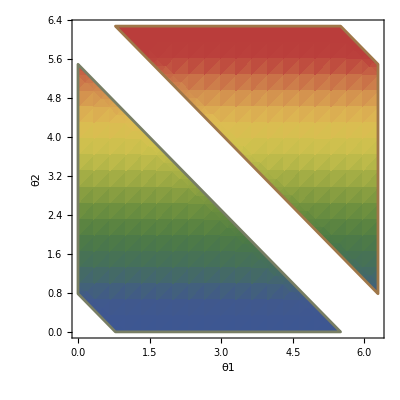

```mathematica
(* ACQ2 overtakes all *)
RegionPlot[{ACQ2norm≥  NEGOnorm && ACQ2norm≥ SQnorm && ACQ2norm≥ ACQ1norm&& ACQ2norm≥ CAP2norm &&  ACQ2norm≥ CAP1norm&&  ACQ2norm≥ WAR1norm && ACQ2norm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

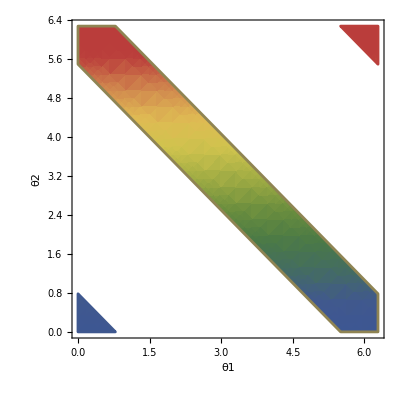

```mathematica
(* WAR1 overtakes all *)
RegionPlot[{WAR1norm≥  NEGOnorm && WAR1norm≥ SQnorm && WAR1norm≥ ACQ1norm&& WAR1norm≥ CAP2norm &&  WAR1norm≥ CAP1norm&&  WAR1norm ≥ ACQ2norm && WAR1norm≥ WAR2norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

```mathematica
(* WAR2 overtakes all *)
RegionPlot[{WAR2norm≥  NEGOnorm && WAR2norm≥ SQnorm && WAR2norm≥ ACQ1norm&& WAR2norm≥ CAP2norm &&  WAR2norm≥ CAP1norm&&  WAR2norm ≥ ACQ2norm && WAR2norm≥ WAR1norm },{θ1,INTEVX,INTEVY},{θ2,INTEVX,INTEVY},AxesLabel->Automatic,PlotRange->All,ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
(* Check min, max, and classical probabilities *)
```

```mathematica
θ1=π;
θ2=π;
{SQnorm,ACQ1norm,ACQ2norm,NEGOnorm,CAP1norm,CAP2norm,WAR1norm,WAR2norm}
```

{0.0985334,0.0766068,0.224657,0.0141443,0.076679,0.117394,0.250272,0.141713}

```mathematica
θ1=0;
θ2=0;
{SQnorm,ACQ1norm,ACQ2norm,NEGOnorm,CAP1norm,CAP2norm,WAR1norm,WAR2norm}
```

{0.0871169,0.0677309,0.198628,0.12837,0.0677947,0.103792,0.221275,0.125293}

```mathematica
θ1=π/2;
θ2=π/2;
{Re[SQnorm],Re[ACQ1norm],Re[ACQ2norm],Re[NEGOnorm],Re[CAP1norm],Re[CAP2norm],Re[WAR1norm],Re[WAR2norm]}
```

{0.122094,0.0949246,0.278376,0.0987181,0.095014,0.0431926,0.0920823,0.175598}